```mathematica
GraphFromSets[sets_]:=Block[{edges={}, i, j, currentBucket,otherVertices},
For[i=1,i<=Length[sets],i++,
currentBucket =sets[[i]];
otherVertices=Flatten[Drop[sets,{i}]];
Table[
Table[
edges=Append[edges,sourceVertex<-> targetVertex]
,
{targetVertex,Select[otherVertices,# >sourceVertex&]}
]
,
{sourceVertex,currentBucket}
]
];
edges
];
```

```mathematica
FindFullFormula[MinimalGraph[5]]
```

{v1x2x3x4x5x6,v1x2x3x46x5,v1x2x36x4x5,v1x2x35x4x6,v1x2x35x46}

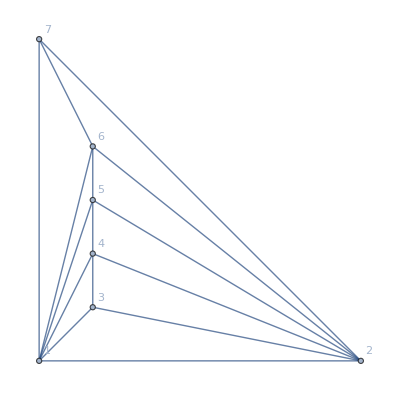
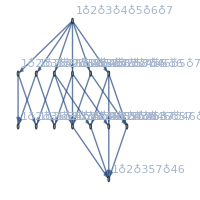
-Graphics-{v1x2x3x4x5x6x7,v1x2x3x4x57x6,v1x2x3x47x5x6,v1x2x3x46x5x7,v1x2x3x46x57,v1x2x37x4x5x6,v1x2x37x46x5,v1x2x36x4x5x7,v1x2x36x4x57,v1x2x36x47x5,v1x2x35x4x6x7,v1x2x357x4x6,v1x2x35x47x6,v1x2x35x46x7,v1x2x357x46}True162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7→-Graphics-

```mathematica
With[
{g=MinimalGraph[6]},
Labeled[Graph[g,GraphLayout->If[PlanarGraphQ[g],"PlanarEmbedding","LayeredDigraphEmbedding"]],{FindFullFormula[ g],PlanarGraphQ[g],ChromaticPolynomial[g,x]},{Left,Top,Bottom}]-> FormulaGraph[FindFullFormula[ g]]
]
```

```mathematica
Table[KSetPartitions[Range[k],4]//Length,{k,4,10}]
```

{1,10,65,350,1701,7770,34105}

```mathematica
EdgeToCouple[e_]:=If[e[[1]]<e[[2]],{e[[1]],e[[2]]},{e[[2]],e[[1]]}]
```

```mathematica
Edges2[g_]:=Sort[Map[EdgeToCouple,EdgeList[g]]]
```

```mathematica
ShowBoth[k_]:=Block[{min=MinimalGraph[k-1], formMin,part, g,diff},
formMin=FindFullFormula[min];
part=SymbolToSets[First[Select[formMin,StringCount[SymbolName[#],"x"]==3&]]];
g=Graph[GraphFromSets[part],VertexLabels->"Name"];
diff=SetDifference[Edges2[g],Edges2[min]];
Column[
{
CompleteBaseCoeff[ChromaticPolynomial[min,x]]-> {Length[formMin],EdgeCount[min],VertexCount[min]}
,
Labeled[Graph[g,GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1,ImageSize->{500,500}, GraphHighlight->Map[UndirectedEdge[#[[1]],#[[2]]]&,diff]],{SetsToSymbol2[part],PlanarGraphQ[g],CompleteBaseCoeff[ ChromaticPolynomial[g,x]]},{Left,Top,Bottom}]-> {Length[FindFullFormula[ g]],EdgeCount[g],VertexCount[g]}
,
diff
}
]
]
```

```mathematica
Table[PadRight[CompleteBaseCoeff[ChromaticPolynomial[MinimalGraph[kk-1],x]],15],{kk,4,10}]//TableForm
```

0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 7 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 15 | 25 | 10 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 31 | 90 | 65 | 15 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 63 | 301 | 350 | 140 | 21 | 1 | 0 | 0 | 0 | 0

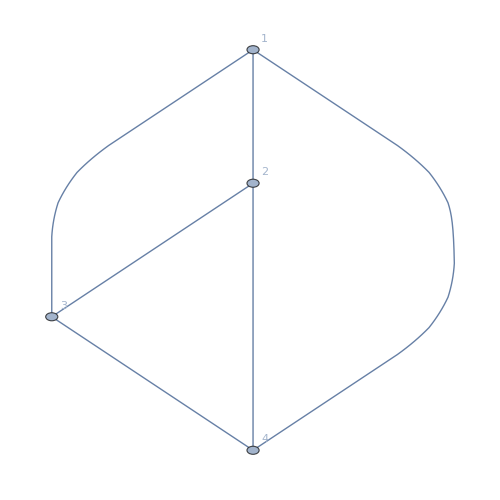
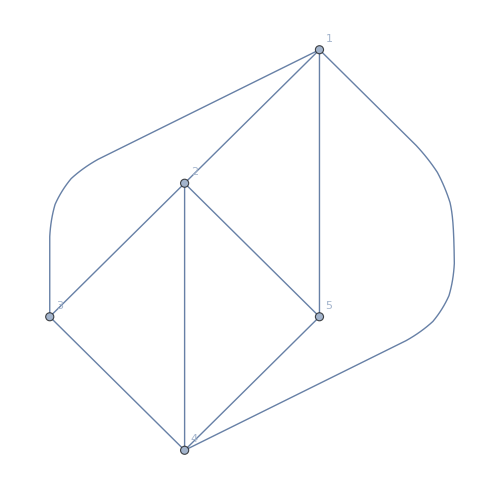
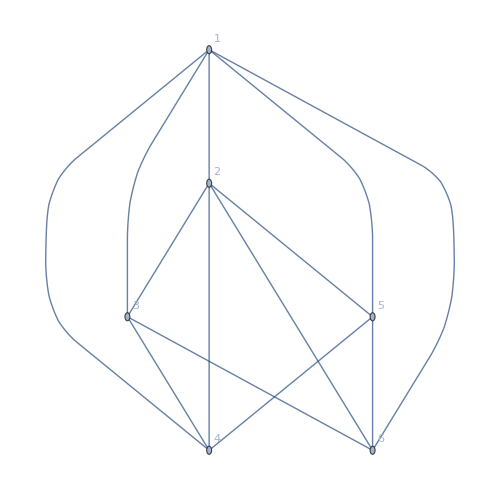
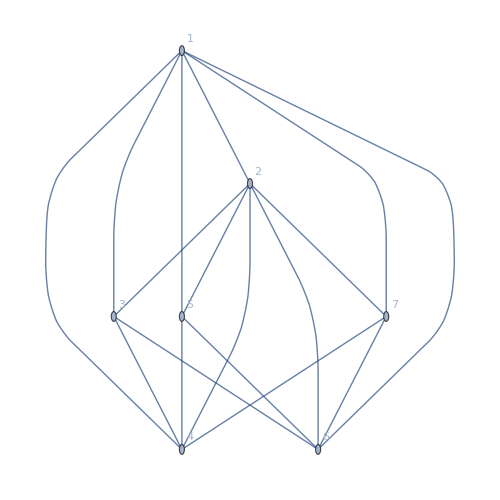
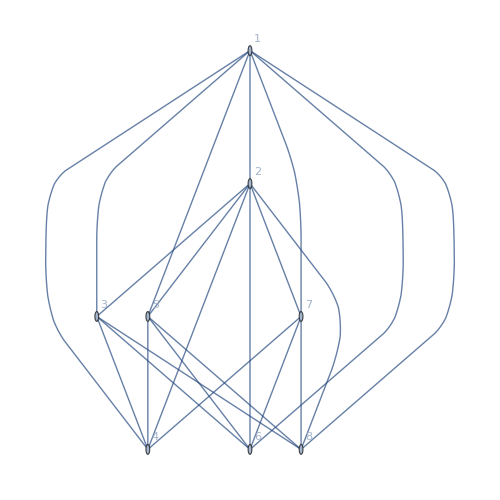
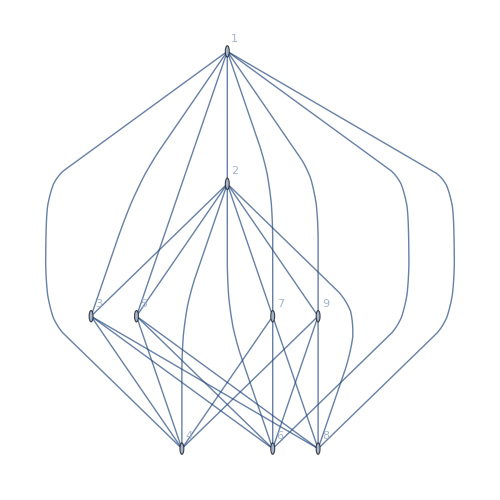
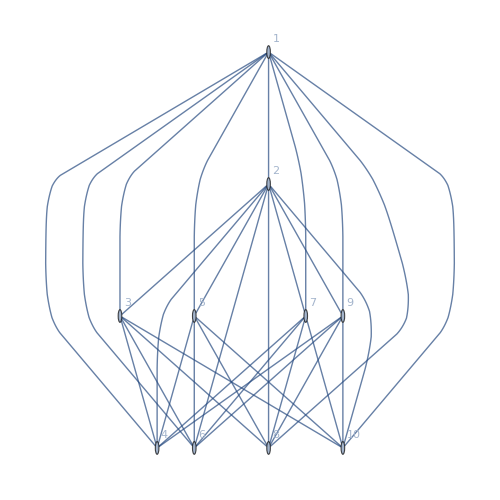
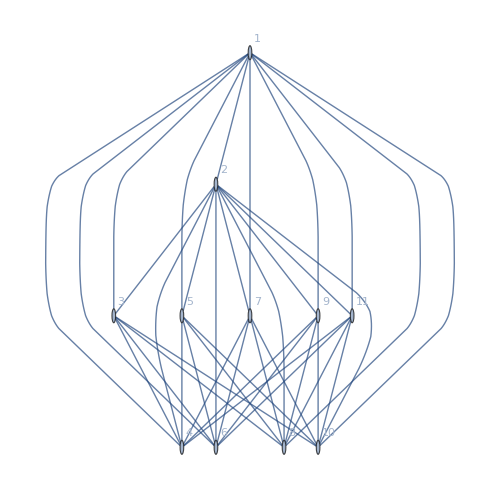
{{0,0,0,0,1}→{1,6,4}
-Graphics-v1x2x3x4True{0,0,0,0,1}→{1,6,4}
{},{0,0,0,0,1,1}→{2,9,5}
-Graphics-v1x2x35x4True{0,0,0,0,1,1}→{2,9,5}
{},{0,0,0,0,1,3,1}→{5,12,6}
-Graphics-v1x2x35x46False{0,0,0,0,1,2,1}→{4,13,6}
{{3,6}},{0,0,0,0,1,7,6,1}→{15,15,7}
-Graphics-v1x2x357x46False{0,0,0,0,1,4,4,1}→{10,17,7}
{{3,6},{4,7}},{0,0,0,0,1,15,25,10,1}→{52,18,8}
-Graphics-v1x2x357x468False{0,0,0,0,1,6,11,6,1}→{25,22,8}
{{3,6},{3,8},{4,7},{5,8}},{0,0,0,0,1,31,90,65,15,1}→{203,21,9}
-Graphics-v1x2x3579x468False{0,0,0,0,1,10,28,26,9,1}→{75,27,9}
{{3,6},{3,8},{4,7},{4,9},{5,8},{6,9}},{0,0,0,0,1,63,301,350,140,21,1}→{877,24,10}
-Graphics-v1x2x3579x468aFalse{0,0,0,0,1,14,61,86,50,12,1}→{225,33,10}
{{3,6},{3,8},{3,10},{4,7},{4,9},{5,8},{5,10},{6,9},{7,10}},{0,0,0,0,1,127,966,1701,1050,266,28,1}→{4140,27,11}
-Graphics-v1x2x3579bx468aFalse{0,0,0,0,1,22,136,276,236,92,16,1}→{780,39,11}
{{3,6},{3,8},{3,10},{4,7},{4,9},{4,11},{5,8},{5,10},{6,9},{6,11},{7,10},{8,11}},{0,0,0,0,1,255,3025,7770,6951,2646,462,36,1}→{21147,30,12}
-Graphics-v1x2x3579bx468acFalse{0,0,0,0,1,30,275,770,927,530,150,20,1}→{2704,46,12}
{{3,6},{3,8},{3,10},{3,12},{4,7},{4,9},{4,11},{5,8},{5,10},{5,12},{6,9},{6,11},{7,10},{7,12},{8,11},{9,12}},{0,0,0,0,1,511,9330,34105,42525,22827,5880,750,45,1}→{115975,33,13}
-Graphics-v1x2x3579bdx468acFalse{0,0,0,0,1,46,580,2200,3551,2782,1130,240,25,1}→{10556,53,13}
{{3,6},{3,8},{3,10},{3,12},{4,7},{4,9},{4,11},{4,13},{5,8},{5,10},{5,12},{6,9},{6,11},{6,13},{7,10},{7,12},{8,11},{8,13},{9,12},{10,13}},{0,0,0,0,1,1023,28501,145750,246730,179487,63987,11880,1155,55,1}→{678570,36,14}
-Graphics-v1x2x3579bdx468aceFalse{0,0,0,0,1,62,1141,5710,12160,12632,6987,2130,355,30,1}→{41209,61,14}
{{3,6},{3,8},{3,10},{3,12},{3,14},{4,7},{4,9},{4,11},{4,13},{5,8},{5,10},{5,12},{5,14},{6,9},{6,11},{6,13},{7,10},{7,12},{7,14},{8,11},{8,13},{9,12},{9,14},{10,13},{11,14}}}

```mathematica
Table[Framed[ShowBoth[kk]],{kk,4,14}]
```

```mathematica
ShowBothShort[k_]:=Block[{min=MinimalGraph[k-1], formMin,part, g},
formMin=FindFullFormula[min];
part=SymbolToSets[First[Select[formMin,StringCount[SymbolName[#],"x"]==3&]]];
g=Graph[GraphFromSets[part],VertexLabels->"Name"];
SetDifference[Edges2[g],Edges2[min]]
]
```

```mathematica
Table[Length[ShowBothShort[kk]],{kk,4,14}]
```

{0,0,1,2,4,6,9,12,16,20,25}

```mathematica
ShowBothShort2[k_]:=Block[{min=MinimalGraph[k-1], formMin,part, g},
formMin=FindFullFormula[min];
part=SymbolToSets[First[Select[formMin,StringCount[SymbolName[#],"x"]==3&]]];
g=GraphFromSets[part];
Length[g]
]
```

```mathematica
Table[ShowBothShort2[kk],{kk,4,14}]
```

{6,9,13,17,22,27,33,39,46,53,61}

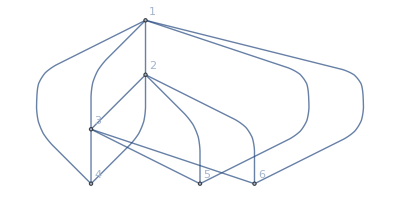
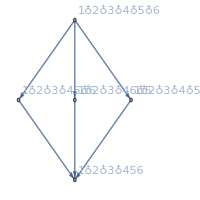
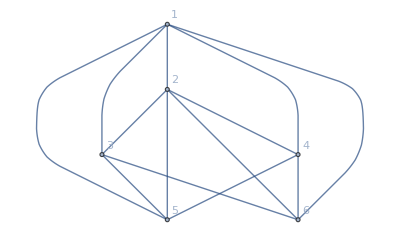
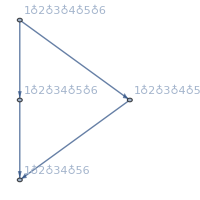
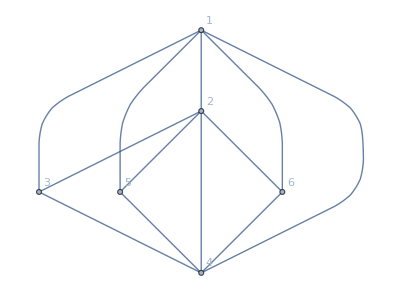
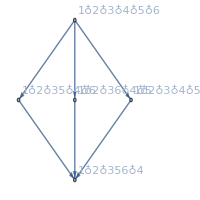
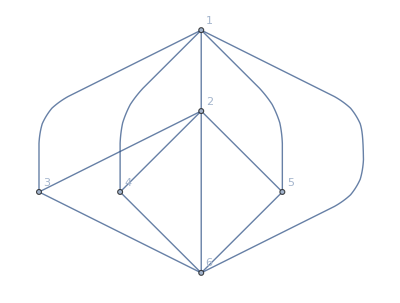
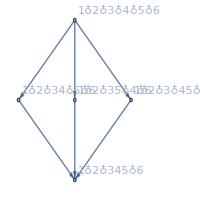
{-Graphics-v1x2x3x456False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x2x34x56False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x2x356x4False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x2x345x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x2x36x45False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x2x346x5False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x2x35x46False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x23x4x56False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x24x3x56False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x256x3x4False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x23x45x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x245x3x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x26x3x45False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x23x46x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x246x3x5False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x25x3x46False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x234x5x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x25x34x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x26x34x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x235x4x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x24x35x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x26x35x4False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x236x4x5False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v1x24x36x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v1x25x36x4False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v12x3x4x56False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v13x2x4x56False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v14x2x3x56False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v156x2x3x4False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v12x3x45x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v13x2x45x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v145x2x3x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v16x2x3x45False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v12x3x46x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v13x2x46x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v146x2x3x5False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v15x2x3x46False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v12x34x5x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v134x2x5x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v15x2x34x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v16x2x34x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v12x35x4x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v135x2x4x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v14x2x35x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v16x2x35x4False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v12x36x4x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v136x2x4x5False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v14x2x36x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v15x2x36x4False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v123x4x5x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v14x23x5x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v15x23x4x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v16x23x4x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v124x3x5x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v13x24x5x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v15x24x3x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v16x24x3x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v125x3x4x6False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v13x25x4x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v14x25x3x6False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v16x25x3x4False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v126x3x4x5False-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6→-Graphics-,-Graphics-v13x26x4x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v14x26x3x5False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-,-Graphics-v15x26x3x4False-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6→-Graphics-}

{2<->3,3<->6}

```mathematica
Table[
With[
{g=Graph[GraphFromSets[part],VertexLabels->"Name"]},
Labeled[Graph[g,GraphLayout->If[PlanarGraphQ[g],"PlanarEmbedding","LayeredDigraphEmbedding"]],{SetsToSymbol[part],PlanarGraphQ[g],ChromaticPolynomial[g,x]},{Left,Top,Bottom}]-> FormulaGraph[FindFullFormula[ g]]
],{part,KSetPartitions[Range[6],4]}]
```

```mathematica
EdgeList[-Graphics-]
```

{1<->2,1<->3,1<->5,1<->4,1<->6,2<->3,2<->5,2<->4,2<->6,3<->4,3<->6,5<->6,4<->5}

```mathematica
EdgeList[-Graphics-]
```

{1<->2,1<->3,3<->2,1<->4,2<->4,3<->4,1<->5,2<->5,4<->5,1<->6,2<->6,5<->6}

```mathematica
SetDifference[Edges2[-Graphics-],Edges2[-Graphics-]]
```

{{3,6}}